Fitting data in Mathematica

set up a set of x,y pairs of data to be fit to

```mathematica
<<"http://www.physics.wisc.edu/~tgwalker/448defs.m"
```

```mathematica
data={{0.01,0},{0.02,0.0000933397},{0.03,0.000180913},{0.04,0.000256975},{0.05,0.000321049},{0.060000000000000005,0.000384855},{0.06999999999999999,0.000461592},{0.08,0.000553127},{0.09,0.000645553},{0.09999999999999999,0.000724471}};
```

Here’s a plot of the data

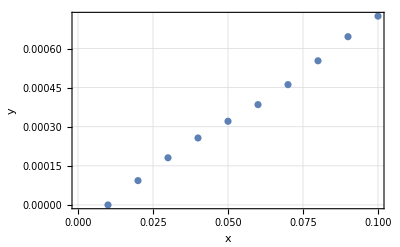

```mathematica
lp=ThadPlot[ListPlot[data,PlotRange->{{0,.1},All}],{"x","y"}]
```

I have a model that I think should describe the data:  y=m (x-x0)+b+c Sin[2π (x-x0)/Λ].  The parameters of the model, to be determined by the fitting, are {m,x0,b,c,Λ}.

```mathematica
model[x_,{m_,x0_,b_,c_,Λ_}]:=m (x-x0)+b+c Sin[2π (x-x0)/Λ]
```

Get a feel for what the model parameters are by guessing:

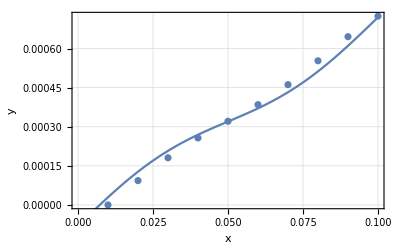

```mathematica
aguess={.008,.05,.00032,-.00005,.1};Show[lp,Plot[model[x,aguess],{x,0,.1}]]
```

This function will adjust the values of the parameters, starting with your guess, to minimize the differences (y_model-y_data)^2.

```mathematica
With[{aa={m,x0,b,c,Λ}},nlm=NonlinearModelFit[data,model[x,aa],{aa,aguess}ᵀ,x]]
```

FittedModel[0.000315814+«20» («1»)-0.000016357 Sin[99.7494 (-«20»+x)]]

To find what the fit parameters are, do this:

```mathematica
a={m,x0,b,c,Λ}/.nlm["BestFitParameters"]
```

{0.00775496,0.0492505,0.000315814,-0.000016357,0.0629897}

Now compare the model to the data:

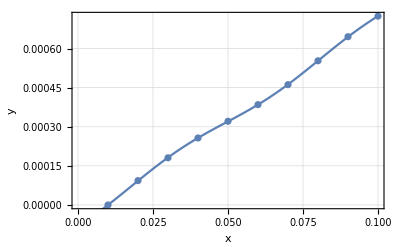

```mathematica
Show[lp,Plot[model[x,a],{x,0,.1}]]
```